## Student Spring Break Behaviors and COVID-19 Transmission

```mathematica
Brenna Mehl, Dawson Brown, Leo Pang, Aidan Holland
```

### Initial Values :

```mathematica
au = 1/7.5; (*recovery rate for unvaccinated indiviuals 1/length of infection*)
av = 1/5.5; (*recovery rate for vaccinated indiviuals, 1/length of infection*)
covidCases= 838/7; (*use first day covid cases*)
numUndergrads = 19742; (*total undergraduates*)
vaxRate = .93; (*proportion vaccinated*)
days = 109; (*number of days in semester*)
p=0.8;(*proportion who go to spring break environment 1*)
tD = .00001 ; (*difference in transmission rate between campus bu/bv and spring break transmission rates*)
campusBu = .000020; (*campus transmission rate to unvaccinated indiviuals*)
campusBv =.000012;(*campus transmission rate to vaccinated indiviuals*)
```

### Campus Transmission Before Spring Break (Days 1-60)

```mathematica
(*Initialize SIR Tables*)
tabSu = Table[0, {i,days}];
tabSv = Table[0, {i,days}];
tabIu = Table[0, {i,days}];
tabIv = Table[0, {i,days}];
tabR = Table[0, {i,days}];
```

```mathematica
(*Iniialize Values*)
su = (numUndergrads-covidCases)(1-vaxRate); (*initial unvaccinated susceptible individuals*)
sv =(numUndergrads-covidCases)(vaxRate ); (*initial vaccinated susceptible individuals*)
iu = covidCases(1-vaxRate); (*initial unvaccinated infected individuals*)
iv =covidCases(vaxRate); (*initial vaccinated infected individuals*)
r =0; (*initial recovered indiviuals, 0 becasuse we assume all students can be infected*)
bu = campusBu; (*transmission rate to an unvaccinated individudal*)
bv = campusBv; (*transmission rate to a vaccinated individual*)
numDays = 60; (*number of days*)
```

```mathematica
(*Run SIR Model*)
 Do[
tabSu[[i]] = su;
tabSv[[i]] = sv;
tabIu[[i]] = iu;
tabIv[[i]] = iv;
tabR[[i]] = r;
s1u=su - bu su(iv + iu);
s1v=sv - bv sv(iv + iu);
i1u = iu+ bu su(iv+iu) - au iu;
i1v = iv+ bv sv(iv+iu) - av iv;
r1 = r + au iu + av iv;
su = s1u;
sv = s1v;
iu = i1u;
iv = i1v;
r = r1,
{i, numDays}];
```

### SIR Plots Before Break

Create Plots:

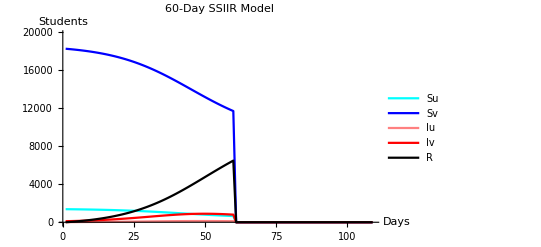

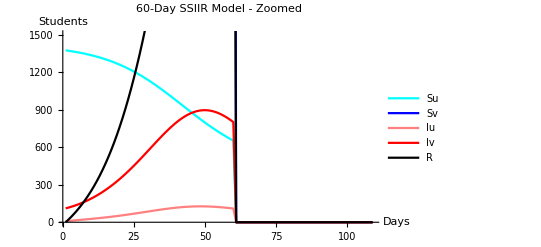

```mathematica
plotSu = ListPlot[tabSu, Joined -> True, PlotStyle -> Cyan, PlotLegends-> {"Su"}];
plotSv = ListPlot[tabSv, Joined -> True, PlotStyle -> Blue, PlotLegends-> {"Sv"}];
plotIu = ListPlot[tabIu, Joined -> True, PlotStyle -> Pink, PlotLegends-> {"Iu"}];
plotIv = ListPlot[tabIv, Joined -> True, PlotStyle -> Red, PlotLegends-> {"Iv"}];
plotR = ListPlot[tabR, Joined -> True, PlotStyle -> Black, PlotLegends-> {"R"}];
Show[plotSu, plotSv, plotIu, plotIv , plotR, PlotRange -> {0,19742}, AxesLabel ->{"Days", "Students"}, PlotLabel-> "60-Day SSIIR Model"]
Show[plotSu, plotSv, plotIu, plotIv , plotR, PlotRange -> {0,1500}, AxesLabel ->{"Days", "Students"}, PlotLabel-> "60-Day SSIIR Model - Zoomed"]
```

### Spring Break Environment 1 (Days 61-69)

```mathematica
(*Initial Values*)
iTabSu =tabSu[[60]];
iTabSv =tabSv[[60]];
iTabIu =tabIu[[60]];
iTabIv =tabIv[[60]];
iTabR=tabR[[60]];
su = iTabSu(p); (*initial unvaccinated susceptible individuals*)
sv =iTabSv(p);(*initial vaccinated susceptible individuals*)
iu = iTabIu(p); (*initial unvaccinated infected individuals*)
iv =iTabIv (p) ;(*initial vaccinated infected individuals*)
r =iTabR(p); (*initial recovered indiviuals*)
bu = campusBu + tD; (*transmission rate to an unvaccinated individudal*)
bv = campusBv +tD ;(*transmission rate to a vaccinated individual*)
numDays = 9; (*number of days*)

(*SIR Model*)
 Do[
tabSu[[i+59]] = su;
tabSv[[i+59]] = sv;
tabIu[[i+59]] = iu;
tabIv[[i+59]] = iv;
tabR[[i+59]] = r;
s1u=su - bu su(iv + iu);
s1v=sv - bv sv(iv + iu);
i1u = iu+ bu su(iv+iu) - au iu;
i1v = iv+ bv sv(iv+iu) - av iv;
r1 = r + au iu + av iv;
su = s1u;
sv = s1v;
iu = i1u;
iv = i1v;
r = r1,
{i, numDays+1}];
```

### Spring Break Environment 2 (Days 61-69)

```mathematica
(*Initial Values*)
su = iTabSu(1-p); (*initial unvaccinated susceptible individuals*)
sv =iTabSv(1-p);(*initial vaccinated susceptible individuals*)
iu = iTabIu(1-p); (*initial unvaccinated infected individuals*)
iv =iTabIv (1-p) ;(*initial vaccinated infected individuals*)
r =iTabR(1-p); (*initial recovered indiviuals*)
bu = campusBu - tD; (*transmission rate to an unvaccinated individudal*)
bv = campusBv -tD; (*transmission rate to a vaccinated individual*)
numDays = 9; (*number of days*)

(*SIR Model*)
 Do[
tabSu[[i+59]] = tabSu[[i+59]]+ su;
tabSv[[i+59]] = tabSv[[i+59]]+ sv;
tabIu[[i+59]] = tabIu[[i+59]]+ iu;
tabIv[[i+59]] = tabIv[[i+59]]+ iv;
tabR[[i+59]] = tabR[[i+59]]+ r;
s1u=su - bu su(iv + iu);
s1v=sv - bv sv(iv + iu);
i1u = iu+ bu su(iv+iu) - au iu;
i1v = iv+ bv sv(iv+iu) - av iv;
r1 = r + au iu + av iv;
su = s1u;
sv = s1v;
iu = i1u;
iv = i1v;
r = r1,
{i, numDays+1}];
```

### SIR Plots After Break

Create Plots:

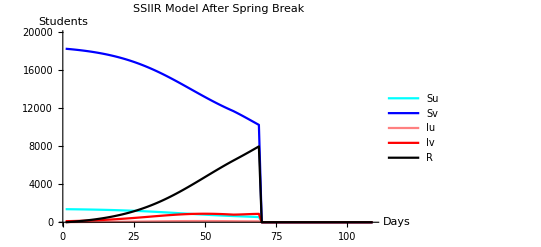

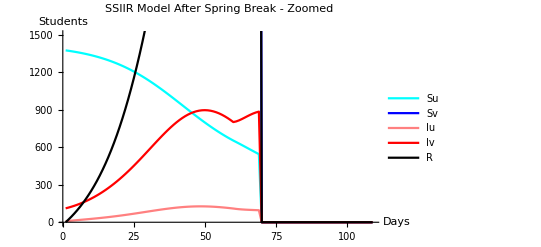

```mathematica
plotSu = ListPlot[tabSu, Joined -> True, PlotStyle -> Cyan, PlotLegends-> {"Su"}];
plotSv = ListPlot[tabSv, Joined -> True, PlotStyle -> Blue, PlotLegends-> {"Sv"}];
plotIu = ListPlot[tabIu, Joined -> True, PlotStyle -> Pink, PlotLegends-> {"Iu"}];
plotIv = ListPlot[tabIv, Joined -> True, PlotStyle -> Red, PlotLegends-> {"Iv"}];
plotR = ListPlot[tabR, Joined -> True, PlotStyle -> Black, PlotLegends-> {"R"}];
Show[plotSu, plotSv, plotIu, plotIv , plotR, PlotRange -> {0,19742}, AxesLabel ->{"Days", "Students"}, PlotLabel-> "SSIIR Model After Spring Break"]
Show[plotSu, plotSv, plotIu, plotIv , plotR, PlotRange -> {0,1500}, AxesLabel ->{"Days", "Students"}, PlotLabel-> "SSIIR Model After Spring Break - Zoomed"]
```

### Campus Transmission After Spring Break (Days 70-109)

```mathematica
(*Initial Values*)
su = tabSu[[69]]; (*initial unvaccinated susceptible individuals*)
sv = tabSv[[69]]; (*initial vaccinated susceptible individuals*)
iu =  tabIu[[69]]; (*initial unvaccinated infected individuals*)
iv =tabIv[[69]]; (*initial vaccinated infected individuals*)
r =tabR[[69]]; (*initial recovered indiviuals*)
bu = campusBu; (*transmission rate to an unvaccinated individudal*)
bv = campusBv; (*transmission rate to a vaccinated individual*)
numDays = days-9-60; (*number of days*)

(*SIRModel*)
 (Do[
tabSu[[i+68]] = su;
tabSv[[i+68]] = sv;
tabIu[[i+68]] = iu;
tabIv[[i+68]] = iv;
tabR[[i+68]] = r;
s1u=su - bu su(iv + iu);
s1v=sv - bv sv(iv + iu);
i1u = iu+ bu su(iv+iu) - au iu;
i1v = iv+ bv sv(iv+iu) - av iv;
r1 = r + au iu + av iv;
su = s1u;
sv = s1v;
iu = i1u;
iv = i1v;
r = r1,
{i, numDays+1}];)
```

### SIR Plots at End of Semester

Create Plots:

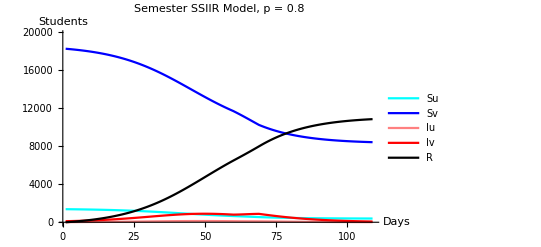

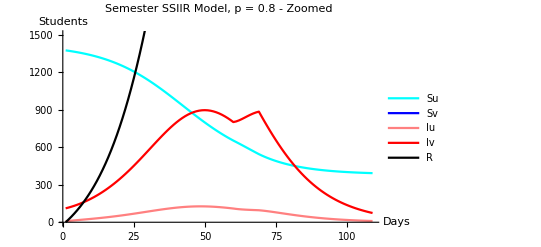

```mathematica
plotSu = ListPlot[tabSu, Joined -> True, PlotStyle -> Cyan, PlotLegends-> {"Su"}];
plotSv = ListPlot[tabSv, Joined -> True, PlotStyle -> Blue, PlotLegends-> {"Sv"}];
plotIu = ListPlot[tabIu, Joined -> True, PlotStyle -> Pink, PlotLegends-> {"Iu"}];
plotIv = ListPlot[tabIv, Joined -> True, PlotStyle -> Red, PlotLegends-> {"Iv"}];
plotR = ListPlot[tabR, Joined -> True, PlotStyle -> Black, PlotLegends-> {"R"}];
Show[plotSu, plotSv, plotIu, plotIv , plotR, PlotRange -> {0,19742}, AxesLabel ->{"Days", "Students"}, PlotLabel-> "Semester SSIIR Model, p = 0.8"]
Show[plotSu, plotSv, plotIu, plotIv , plotR, PlotRange -> {0,1500}, AxesLabel ->{"Days", "Students"}, PlotLabel-> "Semester SSIIR Model, p = 0.8 - Zoomed"]
```

Compare to a Model Where No Spring Break Occurs:

```mathematica
au = 1/7.5; (*recovery rate for unvaccinated indiviuals 1/length of infection*)
av = 1/5.5; (*recovery rate for vaccinated indiviuals, 1/length of infection*)
covidCases= 838/7; (*use first day covid cases*)
numUndergrads = 19742; (*total undergraduates*)
vaxRate = .93; (*proportion vaccinated*)
days = 109; (*number of days in semester*)
campusBu = .000020; (*campus transmission rate to unvaccinated indiviuals*)
campusBv =.000012;(*campus transmission rate to vaccinated indiviuals*)

(*Initialize SIR Tables*)
tabSu = Table[0, {i,days}];
tabSv = Table[0, {i,days}];
tabIu = Table[0, {i,days}];
tabIv = Table[0, {i,days}];
tabR = Table[0, {i,days}];

(*Initialize Values*)
su = (numUndergrads-covidCases)(1-vaxRate); (*initial unvaccinated susceptible individuals*)
sv =(numUndergrads-covidCases)(vaxRate ); (*initial vaccinated susceptible individuals*)
iu = covidCases(1-vaxRate); (*initial unvaccinated infected individuals*)
iv =covidCases(vaxRate); (*initial vaccinated infected individuals*)
r =0; (*initial recovered indiviuals, 0 becasuse we assume all students can be infected*)
bu = campusBu; (*transmission rate to an unvaccinated individudal*)
bv = campusBv; (*transmission rate to a vaccinated individual*)
numDays = 109; (*number of days*)
```

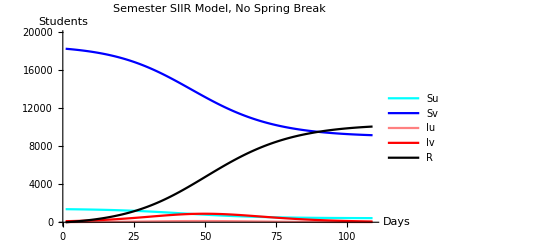

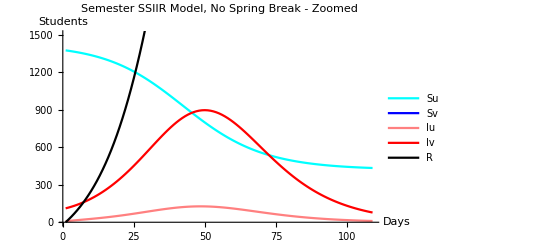

```mathematica
(*Run SIR Model*)
 Do[
tabSu[[i]] = su;
tabSv[[i]] = sv;
tabIu[[i]] = iu;
tabIv[[i]] = iv;
tabR[[i]] = r;
s1u=su - bu su(iv + iu);
s1v=sv - bv sv(iv + iu);
i1u = iu+ bu su(iv+iu) - au iu;
i1v = iv+ bv sv(iv+iu) - av iv;
r1 = r + au iu + av iv;
su = s1u;
sv = s1v;
iu = i1u;
iv = i1v;
r = r1,
{i, numDays}];

plotSu = ListPlot[tabSu, Joined -> True, PlotStyle -> Cyan, PlotLegends-> {"Su"}];
plotSv = ListPlot[tabSv, Joined -> True, PlotStyle -> Blue, PlotLegends-> {"Sv"}];
plotIu = ListPlot[tabIu, Joined -> True, PlotStyle -> Pink, PlotLegends-> {"Iu"}];
plotIv = ListPlot[tabIv, Joined -> True, PlotStyle -> Red, PlotLegends-> {"Iv"}];
plotR = ListPlot[tabR, Joined -> True, PlotStyle -> Black, PlotLegends-> {"R"}];
Show[plotSu, plotSv, plotIu, plotIv , plotR, PlotRange -> {0,19742}, AxesLabel ->{"Days", "Students"}, PlotLabel-> "Semester SIIR Model, No Spring Break"]
rNoBreak = tabR[[109]];
Show[plotSu, plotSv, plotIu, plotIv , plotR, PlotRange -> {0,1500}, AxesLabel ->{"Days", "Students"}, PlotLabel-> "Semester SSIIR Model, No Spring Break - Zoomed"]
```

### Analysis

Creating a Function

```mathematica
(*Creating a Function*)
PModel:=(
	p=0;(*proportion who go to spring break environment 1*)
	tabFinal = Table[0,{i,101}, {j, 2}] ;(*table to hold the p and r values of each run*)
Do[ 
	p =(i-1)/100;
(*Campus Transmission Before Spring Break (Days 1-60)*)
	(*Initialize SIR Tables*)
	tabSu = Table[0, {i,days}];
tabSv = Table[0, {i,days}];
tabIu = Table[0, {i,days}];
tabIv = Table[0, {i,days}];
tabR = Table[0, {i,days}];

(*Initialize Values*)
	su = (numUndergrads-covidCases)(1-vaxRate); (*initial unvaccinated susceptible individuals*)
sv =(numUndergrads-covidCases)(vaxRate ); (*initial vaccinated susceptible individuals*)
iu = covidCases(1-vaxRate); (*initial unvaccinated infected individuals*)
iv =covidCases(vaxRate); (*initial vaccinated infected individuals*)
r =0; (*initial recovered indiviuals, 0 becasuse we assume all students can be infected*)
bu = campusBu; (*transmission rate to an unvaccinated individudal*)
bv = campusBv; (*transmission rate to a vaccinated individual*)
numDays = 60; (*number of days*)


(*SIRModel*)
 Do[
tabSu[[i]] = su;
tabSv[[i]] = sv;
tabIu[[i]] = iu;
tabIv[[i]] = iv;
tabR[[i]] = r;
s1u=su - bu su(iv + iu);
s1v=sv - bv sv(iv + iu);
i1u = iu+ bu su(iv+iu) - au iu;
i1v = iv+ bv sv(iv+iu) - av iv;
r1 = r + au iu + av iv;
su = s1u;
sv = s1v;
iu = i1u;
iv = i1v;
r = r1,
{i, numDays}];

(*Spring Break Environment 1 (Days 61-69)*)
(*Initial Values*)
	su = tabSu[[60]](p); (*initial unvaccinated susceptible individuals*)
sv =tabSv[[60]](p);(*initial vaccinated susceptible individuals*)
iu = tabIu[[60]](p); (*initial unvaccinated infected individuals*)
iv =tabIv[[60]](p) ;(*initial vaccinated infected individuals*)
r =r(p); (*initial recovered indiviuals*)
bu = campusBu + tD; (*transmission rate to an unvaccinated individudal*)
bv = campusBv +tD ;(*transmission rate to a vaccinated individual*)
numDays = 9; (*number of days*)

(*SIR Model*)
 Do[
tabSu[[i+60]] = su;
tabSv[[i+60]] = sv;
tabIu[[i+60]] = iu;
tabIv[[i+60]] = iv;
tabR[[i+60]] = r;
s1u=su - bu su(iv + iu);
s1v=sv - bv sv(iv + iu);
i1u = iu+ bu su(iv+iu) - au iu;
i1v = iv+ bv sv(iv+iu) - av iv;
r1 = r + au iu + av iv;
su = s1u;
sv = s1v;
iu = i1u;
iv = i1v;
r = r1,
{i, numDays}];


(*Spring Break Environment 2 (Days 61-69)*)
(*Initial Values*)
su = tabSu[[60]](1-p); (*initial unvaccinated susceptible individuals*)
sv = tabSv[[60]](1-p); (*initial vaccinated susceptible individuals*)
iu =  tabIu[[60]](1-p); (*initial unvaccinated infected individuals*)
iv =tabIv[[60]](1-p); (*initial vaccinated infected individuals*)
r =tabR[[60]](1-p); (*initial recovered indiviuals*)
bu = campusBu - tD; (*transmission rate to an unvaccinated individudal*)
bv = campusBv -tD; (*transmission rate to a vaccinated individual*)
numDays = 9; (*number of days*)

(*SIR Model*)
 Do[
tabSu[[i+60]] = tabSu[[i+60]]+ su;
tabSv[[i+60]] = tabSv[[i+60]]+ sv;
tabIu[[i+60]] = tabIu[[i+60]]+ iu;
tabIv[[i+60]] = tabIv[[i+60]]+ iv;
tabR[[i+60]] = tabR[[i+60]]+ r;
s1u=su - bu su(iv + iu);
s1v=sv - bv sv(iv + iu);
i1u = iu+ bu su(iv+iu) - au iu;
i1v = iv+ bv sv(iv+iu) - av iv;
r1 = r + au iu + av iv;
su = s1u;
sv = s1v;
iu = i1u;
iv = i1v;
r = r1,
{i, numDays}];

(*Campus Transmission After Spring Break (Days 70-109)*)
(*Initial Values*)
	su = tabSu[[69]]; (*initial unvaccinated susceptible individuals*)
sv = tabSv[[69]]; (*initial vaccinated susceptible individuals*)
iu =  tabIu[[69]]; (*initial unvaccinated infected individuals*)
iv =tabIv[[69]]; (*initial vaccinated infected individuals*)
r =tabR[[69]]; (*initial recovered indiviuals*)
bu = campusBu; (*transmission rate to an unvaccinated individudal*)
bv = campusBv; (*transmission rate to a vaccinated individual*)
numDays = days-9-60; (*number of days*)

(*SIRModel*)
 Do[
tabSu[[i+69]] = su;
tabSv[[i+69]] = sv;
tabIu[[i+69]] = iu;
tabIv[[i+69]] = iv;
tabR[[i+69]] = r;
s1u=su - bu su(iv + iu);
s1v=sv - bv sv(iv + iu);
i1u = iu+ bu su(iv+iu) - au iu;
i1v = iv+ bv sv(iv+iu) - av iv;
r1 = r + au iu + av iv;
su = s1u;
sv = s1v;
iu = i1u;
iv = i1v;
r = r1,
{i, numDays}];
	
	tabFinal[[i,1]] = p;
tabFinal[[i,2]]= tabR[[109]],
{i,101}];
)
```

Running Function, tD = 0.0000100

```mathematica
(*Set Initial Values*)
au = 1/7.5; (*recovery rate for unvaccinated indiviuals*)
av = 1/5.5; (*recovery rate for vaccinated indiviuals*)
covidCases =838/7; (*seven day average of covid cases the first week*)
numUndergrads = 19742; (*total undergraduates*)
vaxRate = .93; (*proportion vaccinated*)
days = 109; (*number of days in semester*)
tD = .00001 ; (*difference in transmission rate between campus bu/bv and spring break transmission rates*)
campusBu = .000020; (*campus transmission rate to unvaccinated indiviuals*)
campusBv =.000012;(*campus transmission rate to vaccinated indiviuals*)

PModel
plotTD1 = ListPlot[tabFinal, Joined -> True, PlotStyle -> Blue,  PlotRange -> {0,19742}, AxesLabel->{"p","students"}, PlotLegends-> {"tD = 0.00001"}];
```

Running Function, tD = 0.0000075

```mathematica
(*Set Initial Values*)
au = 1/7.5; (*recovery rate for unvaccinated indiviuals*)
av = 1/5.5; (*recovery rate for vaccinated indiviuals*)
covidCases =838/7; (*seven day average of covid cases the first week*)
numUndergrads = 19742; (*total undergraduates*)
vaxRate = .93; (*proportion vaccinated*)
days = 109; (*number of days in semester*)
tD = .0000075 ; (*difference in transmission rate between campus bu/bv and spring break transmission rates*)
campusBu = .000020; (*campus transmission rate to unvaccinated indiviuals*)
campusBv =.000012;(*campus transmission rate to vaccinated indiviuals*)

PModel
plotTD75 = ListPlot[tabFinal, Joined -> True, PlotStyle -> Green,  PlotRange -> {0,19742}, AxesLabel->{"p","students"}, PlotLegends-> {"tD = 0.0000075"}];
```

Running Function, tD = 0.0000050

```mathematica
(*Set Initial Values*)
au = 1/7.5; (*recovery rate for unvaccinated indiviuals*)
av = 1/5.5; (*recovery rate for vaccinated indiviuals*)
covidCases =838/7; (*seven day average of covid cases the first week*)
numUndergrads = 19742; (*total undergraduates*)
vaxRate = .93; (*proportion vaccinated*)
days = 109; (*number of days in semester*)
tD = .000005 ; (*difference in transmission rate between campus bu/bv and spring break transmission rates*)
campusBu = .000020; (*campus transmission rate to unvaccinated indiviuals*)
campusBv =.000012;(*campus transmission rate to vaccinated indiviuals*)

PModel
plotTD5 =ListPlot[tabFinal, Joined -> True, PlotStyle -> Red,  PlotRange -> {0,19742}, AxesLabel->{"p","students"},  PlotLegends-> {"tD = 0.000005"}];
```

Running Function, tD = 0.0000025

```mathematica
(*Set Initial Values*)
au = 1/7.5; (*recovery rate for unvaccinated indiviuals*)
av = 1/5.5; (*recovery rate for vaccinated indiviuals*)
covidCases =838/7; (*seven day average of covid cases the first week*)
numUndergrads = 19742; (*total undergraduates*)
vaxRate = .93; (*proportion vaccinated*)
days = 109; (*number of days in semester*)
tD = .0000025 ; (*difference in transmission rate between campus bu/bv and spring break transmission rates*)
campusBu = .000020; (*campus transmission rate to unvaccinated indiviuals*)
campusBv =.000012;(*campus transmission rate to vaccinated indiviuals*)

PModel
plotTD25 =ListPlot[tabFinal, Joined -> True, PlotStyle -> Magenta,  PlotRange -> {0,19742}, AxesLabel->{"p","students"}, PlotLegends-> {"tD = 0.0000025"}];
```

Running Function, tD = 0:

```mathematica
(*Set Initial Values*)
au = 1/7.5; (*recovery rate for unvaccinated indiviuals*)
av = 1/5.5; (*recovery rate for vaccinated indiviuals*)
covidCases =838/7; (*seven day average of covid cases the first week*)
numUndergrads = 19742; (*total undergraduates*)
vaxRate = .93; (*proportion vaccinated*)
days = 109; (*number of days in semester*)
tD = 0 ; (*difference in transmission rate between campus bu/bv and spring break transmission rates*)
campusBu = .000020; (*campus transmission rate to unvaccinated indiviuals*)
campusBv =.000012;(*campus transmission rate to vaccinated indiviuals*)

PModel
plotTD0 =ListPlot[tabFinal, Joined -> True, PlotStyle -> Black,  PlotRange -> {0,19742},  AxesLabel->{"p","students"}, PlotLegends-> {"tD = 0"}];
```

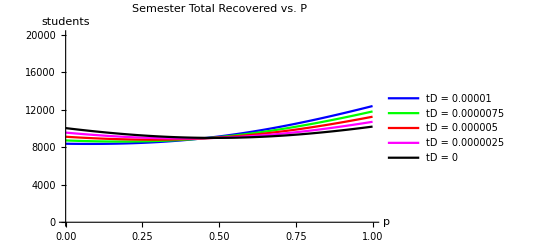

```mathematica
Show[plotTD1, plotTD75, plotTD5, plotTD25,plotTD0,PlotLabel->"Semester Total Recovered vs. P", AxesLabel->{"p","students"},PlotRange ->{0, 20000}]
```

```mathematica
plotNoBreak = Plot[rNoBreak,{x,0,1}, PlotStyle-> Dashed, PlotLegends->{"No Spring Break"}];
```

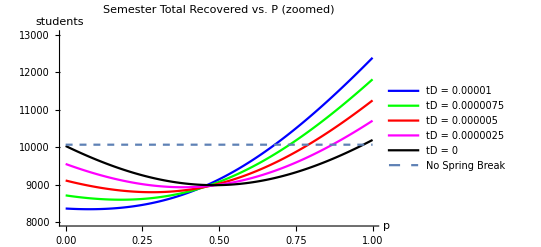

```mathematica
Show[plotTD1, plotTD75, plotTD5, plotTD25, plotTD0, plotNoBreak,PlotLabel->"Semester Total Recovered vs. P (zoomed)", AxesLabel->{"p","students"},PlotRange ->{8000, 13000}]
```